Grid Command Module

```mathematica
(*It is used to join multiple plots together with a common axis "ALWAYS RUN FIRST!!"*)
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

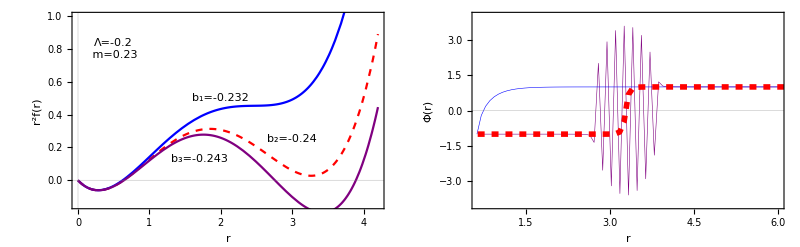

fig1.pdf

```mathematica
(*Figure 1: Plot of three different behaviours of the metric and their field configurations*)
Clear[b,ll];
b=-0.24; ll=-0.2;m=0.23;(*parameters leading to a stable solution*)
gr=-2 m r+r^2+2 b r^3 - ll r^4 /3;
plgr1=Plot[gr,{r,0,4.2}, PlotTheme->"Scientific",PlotStyle->{Red,Dashed},Frame->True,FrameLabel-> {"r","r^2f(r)"},BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Medium]];
roots=NSolve [r^2-2 m r+2 b r^3 - ll r^4 /3==0,r];
r1=roots[[2,1,2]];
rmin=r1;
rmax=16;
imax=200;
dx=(rmax-rmin)/imax;
r[i_]:=i dx+rmin;
fp[i_]:=(f[i]-f[i-1])/dx;
e[i_]:=(r[i]^2 -2m r[i]+2 b r[i]^3-(ll/3) r[i]^4)fp[i]^2+r[i]^2(f[i]^2-1)^2 /2;
f[0]=-1;
f[imax]=1;
etot=dx  Sum[e[i],{i,1,imax}];
r0=10;
ft[x_]:=Tanh[5(x-r0)];
ftab=Table[{f[i],ft[r[i]]},{i,1,imax-1}];
sol1=FindMinimum[etot,ftab,MaxIterations->1000000,AccuracyGoal->6];
etot /. sol1[[2]];
tfsol=Table[{i dx+rmin,f[i]/. sol1[[2]]},{i,0,imax}];
plf2=ListPlot[tfsol,Joined->True,PlotRange->{{r1,6},{-4,4}},Frame->True, PlotTheme->"Scientific",PlotStyle->{Red,Dashed,,Thickness[0.01]},BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Large],FrameLabel->{"r","Φ(r)"}];

Clear[b,ll];
b=-0.232; ll=-0.2;m=0.23;(*parameters leading to collapse*)
gr=-2 m r+r^2+2 b r^3 - ll r^4 /3;
plgr2=Plot[gr,{r,0,4.2}, PlotTheme->"Scientific",PlotStyle->{Blue},Frame->True,FrameLabel-> {"r","r^2f(r)"},BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Medium]];
roots=NSolve [r^2-2 m r+2 b r^3 - ll r^4 /3==0,r];
r1=roots[[2,1,2]];
rmin=r1;
rmax=16;
imax=200;
dx=(rmax-rmin)/imax;
r[i_]:=i dx+rmin;
fp[i_]:=(f[i]-f[i-1])/dx;
e[i_]:=(r[i]^2 -2m r[i]+2 b r[i]^3-(ll/3) r[i]^4)fp[i]^2+r[i]^2(f[i]^2-1)^2 /2;
f[0]=-1;
f[imax]=1;
etot=dx  Sum[e[i],{i,1,imax}];
r0=10;
ft[x_]:=Tanh[5(x-r0)];
ftab=Table[{f[i],ft[r[i]]},{i,1,imax-1}];
sol1=FindMinimum[etot,ftab,MaxIterations->1000000,AccuracyGoal->6];
etot /. sol1[[2]];
tfsol=Table[{i dx+rmin,f[i]/. sol1[[2]]},{i,0,imax}];
plf1=ListPlot[tfsol,Joined->True,PlotRange->{{r1,6},{-4,4}},Frame->True, PlotTheme->"Scientific",PlotStyle->{Blue,Thickness[0.001]},BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Large],FrameLabel->{"r","Φ(r)"}];


Clear[b,ll];
b=-0.243; ll=-0.2;m=0.23;(*parameters leading to ghost instabilities*)
gr=-2 m r+r^2+2 b r^3 - ll r^4 /3;
plgr3=Plot[gr,{r,0,4.2}, PlotTheme->"Scientific",PlotStyle->{Purple},Frame->True,FrameLabel-> {"r","r^2f(r)"},BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Medium]];roots=NSolve [r^2-2 m r+2 b r^3 - ll r^4 /3==0,r];
r1=roots[[2,1,2]];
rmin=r1;
rmax=16;
imax=200;
dx=(rmax-rmin)/imax;
r[i_]:=i dx+rmin;
fp[i_]:=(f[i]-f[i-1])/dx;
e[i_]:=(r[i]^2 -2m r[i]+2 b r[i]^3-(ll/3) r[i]^4)fp[i]^2+r[i]^2(f[i]^2-1)^2 /2;
f[0]=-1;
f[imax]=1;
etot=dx  Sum[e[i],{i,1,imax}];
r0=10;
ft[x_]:=Tanh[5(x-r0)];
ftab=Table[{f[i],ft[r[i]]},{i,1,imax-1}];
sol1=FindMinimum[etot,ftab,MaxIterations->1000000,AccuracyGoal->6];
etot /. sol1[[2]];
tfsol=Table[{i dx+rmin,f[i]/. sol1[[2]]},{i,0,imax}];
plf3=ListPlot[tfsol,Joined->True,PlotRange->{{r1,6},{-4,4}},Frame->True, PlotTheme->"Scientific",PlotStyle->{Purple,Thickness[0.001]},BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Large],FrameLabel->{"r","Φ(r)"}];

panel3=Show[plgr1,plgr2,plgr3,Graphics[Inset["b_1=-0.232",{2,0.5}]],Graphics[Inset["b_2=-0.24",{3,0.25}]],Graphics[Inset["b_3=-0.243",{1.7,0.13}]],Graphics[Inset["Λ=-0.2\n m=0.23",{0.5,0.8}]],BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Medium],PlotRange->{-0.15,1}];
panel4=Show[plf3,plf1,plf2, PlotTheme->"Scientific",PlotStyle->{Purple},BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Medium]];
fig2=Panel[GraphicsGrid[{{panel3,panel4}},Spacings->{0,0},ImageSize->Full],Background->White]
SetDirectory[NotebookDirectory[]];
Export["fig1.pdf",fig2,ImageResolution->1000,ImageSize->Full]
```

FittedModel[Tanh[2.89488 (-3.84766+r)]]

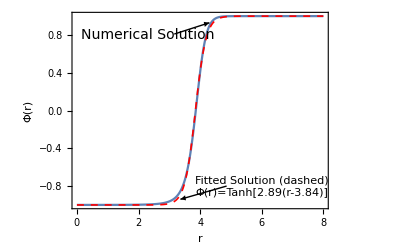

fig2.pdf

```mathematica
(*Figure 2: PLot of a field configuration and its corresponding analytic fit*)
b=-0.212; ll=-0.14;
Clear[f,ft,ftab];
imax=400;
rmin=0.0;
rmax=8;
dx=(rmax-rmin)/imax;
r[i_]:=i dx+rmin;
fp[i_]:=(f[i]-f[i-1])/dx;
e[i_]:=(r[i]^2 + 2 b r[i]^3-(ll/3) r[i]^4)fp[i]^2/2+r[i]^2(f[i]^2-1)^2 /4;
f[0]=-1;
f[imax]=1;
etot=dx  Sum[e[i],{i,1,imax}];
r0=10;
ft[x_]:=Tanh[5(x-r0)];
ftab=Table[{f[i],ft[r[i]]},{i,1,imax-1}];
sol1=FindMinimum[etot,ftab,MaxIterations->1000000,AccuracyGoal->6];
etot /. sol1[[2]];
tfsol=Table[{i dx+rmin,f[i]/. sol1[[2]]},{i,0,imax}];
plsol1=ListPlot[tfsol,Joined->True,PlotRange->All,Frame->True,FrameLabel->{r,Φ}];
Clear[a,r0];
nlm=NonlinearModelFit[tfsol,Tanh[a (r-r0)],{a,r0},r](*Fitted Solution using Φ(r)=Tanh[q(r-Subscript[r, 0])]*)
fapprox=Show[ListPlot[tfsol,Joined->True],Plot[nlm[x],{x,rmin,rmax},PlotTheme->"Scientific",PlotStyle->{Red,Dashed,Thickness[0.003]}],Graphics[{Inset["Numerical Solution",{2.3,.8}]}],Graphics[{Arrow[{{3.16,0.81},{4.3,0.93}}]}],Graphics[{Inset["Fitted Solution (dashed)\nΦ(r)=Tanh[2.89(r-3.84)]",{6,-.8}]}],Graphics[{Arrow[{{4.86,-0.8},{3.36,-0.94}}]}],PlotRange->{{0,8},{1,-1}},PlotTheme->"Scientific",PlotLabel-> None,BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Large],Frame->True,FrameLabel-> {"r","Φ(r)"}]
SetDirectory[NotebookDirectory[]]
Export["fig2.pdf",fapprox,ImageResolution->1000,ImageSize->Large]
```

```mathematica
(*Figure 3: Plots of a 3d metastable field configuration and its density*)
Clear[b,ll];
b=-0.255; ll=-0.202;
Clear[v,f,h,h1]; (* this is a good choice of parameters starting exactly  on the static solution and staying there *)
Vphi[t_,x_]=(f[t,x]^2-1)^2/4;
V[t_,x_]=Vphi[t,x];
dV[t_,x_]=D[Vphi[t,x],f[t,x]];
dd=1+2 b r -ll r^2/3 ;
pde={D[f[t,r],t] ==g[t,r],r^2 D[g[t,r],t]/dd== D[r^2 dd D[f[t,r],r],r]-dV[t,r] r^2};
rmin=0.1;
rmax=15;
r0=3.3;
tmax=800;
h[t_,r_]=Tanh[3(r-r0)];
h1[t_,r_]=D[h[t,r],t]; (* time derivative of h[t,x] *)
bc={f[0,r]==h[0,r],
g[0,r]==h1[0,r],f[t,rmin]==-1,g[t,rmin]==0,f[t,rmax]==1,g[t,rmax]==0};
solution=NDSolve[{pde,bc},{f,g},{r,rmin,rmax},{t,0,tmax},StartingStepSize->{Automatic,rmax/30},PrecisionGoal->2];
fsol0[t_,r_]:=f[t,r] /. solution;
field=RevolutionPlot3D[fsol0[100,rr][[1]],{rr,0.1,6},PlotRange->All,ColorFunction->Function[{x,y,z,t,θ,r},ColorData["Rainbow"][r]],PlotTheme->"Scientific",AxesLabel->{"x","y","Φ(r)"}];(*Plot of the field*)
Clear[rho1,tt]
fmet[r_]:=(1 + 2 b r-(ll/3) r^2);
rho1[tt_,rr_]:=Part[0.5 fmet[r] D[fsol0[t,r],r]^2+(fsol0[t,r]^2-1)^2 /4  /. {t->tt,r->rr},1];
rho1[0.1,rmin];
density=RevolutionPlot3D[rho1[100,rr],{rr,0.1,6},PlotRange->All,ColorFunction->Function[{x,y,z,t,θ,r},ColorData["Rainbow"][r]],PlotTheme->"Scientific",AxesLabel->{"x","y","ρ(r)"}];(*Density plot*)
```

```mathematica
grid3d=Panel[GraphicsGrid[{{field,density}},Spacings->{0,0},ImageSize->Full],Background->White]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["fig3.pdf",grid3d,ImageResolution->1000,ImageSize->Full]
```

fig3.pdf

```mathematica
(*Stability range with m=0*)
```

```mathematica
alistrangemin={{-0.02,-0.07698},{-0.03,-0.0942809},{-0.04,-0.108866},{-0.05,-0.121716},{-0.06,-0.133333},{-0.07,-0.144016},{-0.08,-0.15396},{-0.09,-0.163299},{-0.1,-0.172133},{-0.11,-0.180534},{-0.12,-0.188562},{-0.13,-0.196261},{-0.14,-0.20367},{-0.15,-0.210819},{-0.16,-0.217732},{-0.17,-0.224433},{-0.18,-0.23094},{-0.19,-0.237268},{-0.2,-0.243432},{-0.21,-0.249444},{-0.22,-0.255314},{-0.23,-0.261052},{-0.24,-0.266667},{-0.25,-0.272166},{-0.26,-0.277555},{-0.27,-0.282843},{-0.28,-0.288033},{-0.29,-0.293131},{-0.3,-0.298142},{-0.31,-0.303071},{-0.32,-0.30792},{-0.33,-0.312694},{-0.34,-0.317397},{-0.35,-0.322031},{-0.36,-0.326599},{-0.37,-0.331104},{-0.38,-0.335548},{-0.39,-0.339935},{-0.4,-0.344265},{-0.41,-0.348542},{-0.42,-0.352767},{-0.43,-0.356942},{-0.44,-0.361068},{-0.45,-0.365148},{-0.46,-0.369183},{-0.47,-0.373175},{-0.48,-0.377124},{-0.49,-0.381032},{-0.5,-0.3849},{-0.51,-0.38873},{-0.52,-0.392523},{-0.53,-0.396279},{-0.54,-0.4},{-0.55,-0.403687},{-0.56,-0.40734},{-0.57,-0.410961},{-0.58,-0.41455},{-0.59,-0.418109},{-0.6,-0.421637}};(*List of parameters corresponding to the upper theoretical limit*)
listbrangemax={{-0.02,-0.0816497},{-0.03,-0.1},{-0.04,-0.11547},{-0.05,-0.129099},{-0.06,-0.141421},{-0.07,-0.152753},{-0.08,-0.163299},{-0.09,-0.173205},{-0.1,-0.182574},{-0.11,-0.191485},{-0.12,-0.2},{-0.13,-0.208167},{-0.14,-0.216025},{-0.15,-0.223607},{-0.16,-0.23094},{-0.17,-0.238048},{-0.18,-0.244949},{-0.19,-0.251661},{-0.2,-0.258199},{-0.21,-0.264575},{-0.22,-0.270801},{-0.23,-0.276887},{-0.24,-0.282843},{-0.25,-0.288675},{-0.26,-0.294392},{-0.27,-0.3},{-0.28,-0.305505},{-0.29,-0.310913},{-0.3,-0.316228},{-0.31,-0.321455},{-0.32,-0.326599},{-0.33,-0.331662},{-0.34,-0.33665},{-0.35,-0.341565},{-0.36,-0.34641},{-0.37,-0.351188},{-0.38,-0.355903},{-0.39,-0.360555},{-0.4,-0.365148},{-0.41,-0.369685},{-0.42,-0.374166},{-0.43,-0.378594},{-0.44,-0.382971},{-0.45,-0.387298},{-0.46,-0.391578},{-0.47,-0.395811},{-0.48,-0.4},{-0.49,-0.404145},{-0.5,-0.408248},{-0.51,-0.412311},{-0.52,-0.416333},{-0.53,-0.420317},{-0.54,-0.424264},{-0.55,-0.428174},{-0.56,-0.432049},{-0.57,-0.43589},{-0.58,-0.439697},{-0.59,-0.443471},{-0.6,-0.447214}};(*List of parameters corresponding to the lower limit of metastable solutions*)
lista05={{-0.02,-0.07998},{-0.03,-0.0979809},{-0.04,-0.113166},{-0.05,-0.126516},{-0.06,-0.138533},{-0.07,-0.149616},{-0.08,-0.15996},{-0.09,-0.169699},{-0.1,-0.178833},{-0.11,-0.187534},{-0.12,-0.195962},{-0.13,-0.203961},{-0.14,-0.21167},{-0.15,-0.219119},{-0.16,-0.226232},{-0.17,-0.233233},{-0.18,-0.24004},{-0.19,-0.246568},{-0.2,-0.253032},{-0.21,-0.259244},{-0.22,-0.265414},{-0.23,-0.271352},{-0.24,-0.277167},{-0.25,-0.282966},{-0.26,-0.288555},{-0.27,-0.294043},{-0.28,-0.299433},{-0.29,-0.304831},{-0.3,-0.310042},{-0.31,-0.315171},{-0.32,-0.32022},{-0.33,-0.325194},{-0.34,-0.330097},{-0.35,-0.334931},{-0.36,-0.339699},{-0.37,-0.344404},{-0.38,-0.349048},{-0.39,-0.353635},{-0.4,-0.358165},{-0.41,-0.362642},{-0.42,-0.367067},{-0.43,-0.371442},{-0.44,-0.375768},{-0.45,-0.379948},{-0.46,-0.384183},{-0.47,-0.388375},{-0.48,-0.392524},{-0.49,-0.396632},{-0.5,-0.4006},{-0.51,-0.40463},{-0.52,-0.408623},{-0.53,-0.412579},{-0.54,-0.4165},{-0.55,-0.420287},{-0.56,-0.42414},{-0.57,-0.427961},{-0.58,-0.43165},{-0.59,-0.435409},{-0.6,-0.439137}};(*List of parameters corresponding to the upper limit of metastalble solutions for Backreaction parameter equal to 0.5*)
lista1={{-0.02,-0.07998},{-0.03,-0.0978809},{-0.04,-0.112966},{-0.05,-0.126416},{-0.06,-0.138333},{-0.07,-0.149416},{-0.08,-0.15976},{-0.09,-0.169399},{-0.1,-0.178533},{-0.11,-0.187234},{-0.12,-0.195562},{-0.13,-0.203561},{-0.14,-0.21127},{-0.15,-0.218619},{-0.16,-0.225832},{-0.17,-0.232733},{-0.18,-0.23954},{-0.19,-0.246068},{-0.2,-0.252432},{-0.21,-0.258644},{-0.22,-0.264714},{-0.23,-0.270752},{-0.24,-0.276567},{-0.25,-0.282266},{-0.26,-0.287855},{-0.27,-0.293243},{-0.28,-0.298633},{-0.29,-0.303931},{-0.3,-0.309142},{-0.31,-0.314271},{-0.32,-0.31932},{-0.33,-0.324294},{-0.34,-0.329097},{-0.35,-0.333931},{-0.36,-0.338699},{-0.37,-0.343304},{-0.38,-0.347948},{-0.39,-0.352535},{-0.4,-0.356965},{-0.41,-0.361442},{-0.42,-0.365867},{-0.43,-0.370142},{-0.44,-0.374468},{-0.45,-0.378648},{-0.46,-0.382883},{-0.47,-0.386975},{-0.48,-0.391124},{-0.49,-0.395132},{-0.5,-0.3992},{-0.51,-0.40313},{-0.52,-0.407123},{-0.53,-0.410979},{-0.54,-0.4149}};(*List of parameters corresponding to the upper limit of metastalble solutions for Backreaction parameter equal to 1*)
lista0={{-0.02,-0.08008},{-0.03,-0.0980809},{-0.04,-0.113266},{-0.05,-0.126616},{-0.06,-0.138733},{-0.07,-0.149816},{-0.08,-0.16016},{-0.09,-0.169899},{-0.1,-0.179133},{-0.11,-0.187934},{-0.12,-0.196262},{-0.13,-0.204261},{-0.14,-0.21207},{-0.15,-0.219519},{-0.16,-0.226732},{-0.17,-0.233733},{-0.18,-0.24054},{-0.19,-0.247168},{-0.2,-0.253532},{-0.21,-0.259844},{-0.22,-0.266014},{-0.23,-0.272052},{-0.24,-0.277867},{-0.25,-0.283666},{-0.26,-0.289255},{-0.27,-0.294843},{-0.28,-0.300233},{-0.29,-0.305631},{-0.3,-0.310842},{-0.31,-0.316071},{-0.32,-0.32112},{-0.33,-0.326094},{-0.34,-0.331097},{-0.35,-0.335931},{-0.36,-0.340699},{-0.37,-0.345504},{-0.38,-0.350148},{-0.39,-0.354735},{-0.4,-0.359265},{-0.41,-0.363842},{-0.42,-0.368267},{-0.43,-0.372642},{-0.44,-0.376968},{-0.45,-0.381248},{-0.46,-0.385483},{-0.47,-0.389675},{-0.48,-0.393924},{-0.49,-0.398032},{-0.5,-0.4021},{-0.51,-0.40613},{-0.52,-0.410123},{-0.53,-0.414079},{-0.54,-0.418},{-0.55,-0.421887},{-0.56,-0.42574},{-0.57,-0.429561},{-0.58,-0.43335},{-0.59,-0.437109},{-0.6,-0.440837}};(*List of parameters corresponding to the upper limit of metastalble solutions for zero Backreaction*)
```

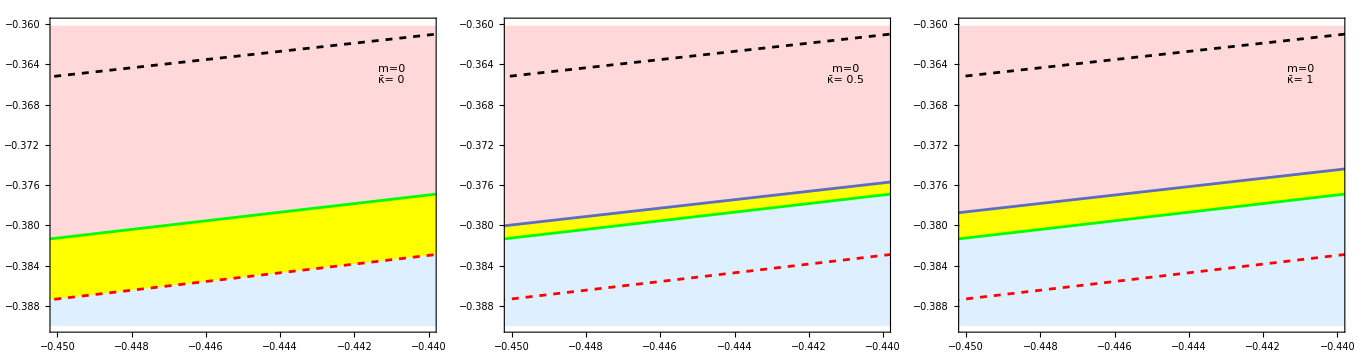
-Graphics-Λb

D:\Downloads

fig4.pdf

```mathematica
p[1]=Show[ListLinePlot[{Sort[alistrangemin],Sort[lista0],Sort[listbrangemax]},Frame->True,PlotStyle->{{Dashed,Black,Thickness[0.005]},{Green,Thickness[0.005]},{Dashed,Red,Thickness[0.005]}},PlotRange->{{-.45,-.44},{-.39,-.36}},PlotTheme->"Scientific",Filling->{{2->{{3},Yellow}},{2->{Axis,LightRed},3->{Bottom,LightBlue}}}],Graphics[{Inset["m=0\nκ̄= 0",{-.441,-.3650}]}],BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14]];
p[2]=Show[ListLinePlot[{Sort[alistrangemin],Sort[lista05],Sort[listbrangemin],Sort[listbrangemax]},Frame->True,PlotStyle->{{Dashed,Black,Thickness[0.005]},Thickness[0.005],{Green,Thickness[0.005]},{Dashed,Red,Thickness[0.005]}},PlotRange->{{-.45,-.44},{-.39,-.36}},PlotTheme->"Scientific",Filling->{{2->{{3},Yellow}},{2->{Axis,LightRed},3->{Bottom,LightBlue}}}],Graphics[{Inset["m=0\nκ̄= 0.5",{-.441,-.3650}]}],BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14]];
p[3]=Show[ListLinePlot[{Sort[alistrangemin],Sort[lista1],Sort[listbrangemin],Sort[listbrangemax]},Frame->True,PlotStyle->{{Dashed,Black,Thickness[0.005]},Thickness[0.005],{Green,Thickness[0.005]},{Dashed,Red,Thickness[0.005]}},PlotRange->{{-.45,-.44},{-.39,-.36}},PlotTheme->"Scientific",Filling->{{2->{{3},Yellow}},{2->{Axis,LightRed},3->{Bottom,LightBlue}}}],Graphics[{Inset["m=0\nκ̄= 1",{-.441,-.3650}]}],BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14]];
grid=Panel[GraphicsGrid[{{p[1],p[2],p[3]}},Spacings->{0,0},ImageSize->Full],{"Λ",Rotate["b",Pi/2]},{Bottom,Left},Background->White];
grid1=Table[p[i],{m,1},{i,1,3}];

k1=Panel[plotGrid[grid1,1363,363],{"Λ",Rotate["b",Pi/2]},{Bottom,Left},Background->White]
SetDirectory[NotebookDirectory[]]
Export["fig4.pdf",k1,ImageResolution->1000,ImageSize->Scaled[4]]
```

```mathematica
(*Stability range with m=0.1*)
```

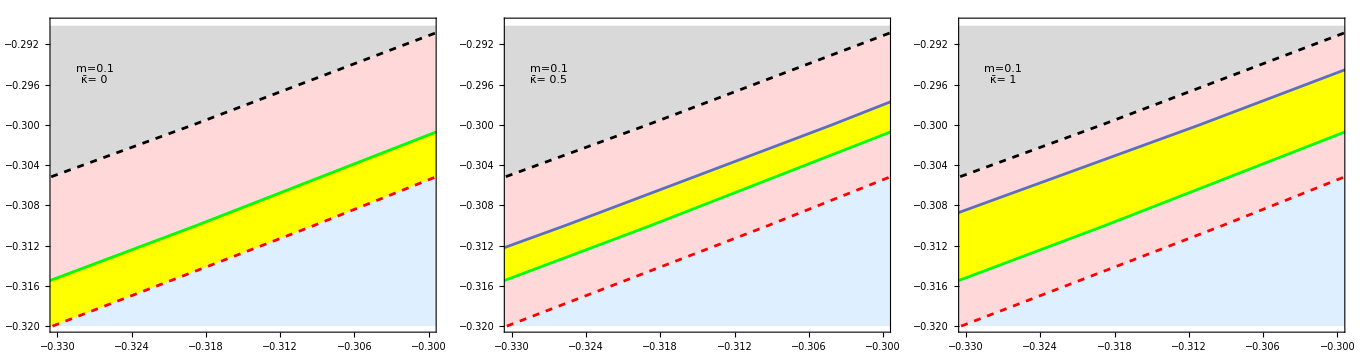
-Graphics-Λb

D:\Downloads

fig5.pdf

```mathematica
alistllrangemin={{-0.0218665,-0.08},{-0.0277182,-0.09},{-0.0342741,-0.1},{-0.0415376,-0.11},{-0.0495123,-0.12},{-0.0582016,-0.13},{-0.0676093,-0.14},{-0.0777389,-0.15},{-0.0885944,-0.16},{-0.100179,-0.17},{-0.112498,-0.18},{-0.125554,-0.19},{-0.139351,-0.2},{-0.153894,-0.21},{-0.169186,-0.22},{-0.185232,-0.23},{-0.202035,-0.24},{-0.219602,-0.25},{-0.237935,-0.26},{-0.257039,-0.27},{-0.276919,-0.28},{-0.29758,-0.29},{-0.319025,-0.3},{-0.341261,-0.31},{-0.364292,-0.32},{-0.388122,-0.33},{-0.412758,-0.34},{-0.438204,-0.35},{-0.464466,-0.36},{-0.491548,-0.37},{-0.519457,-0.38},{-0.548199,-0.39},{-0.577778,-0.4},{-0.608201,-0.41}};(*List of parameters corresponding to the upper theoretical limit*)
listllrangemax={{-0.0195188,-0.08},{-0.0247561,-0.09},{-0.0306287,-0.1},{-0.037141,-0.11},{-0.0442972,-0.12},{-0.0521019,-0.13},{-0.0605598,-0.14},{-0.0696755,-0.15},{-0.0794537,-0.16},{-0.0898995,-0.17},{-0.101018,-0.18},{-0.112814,-0.19},{-0.125292,-0.2},{-0.138459,-0.21},{-0.15232,-0.22},{-0.166881,-0.23},{-0.182146,-0.24},{-0.198122,-0.25},{-0.214816,-0.26},{-0.232233,-0.27},{-0.25038,-0.28},{-0.269263,-0.29},{-0.288889,-0.3},{-0.309265,-0.31},{-0.330398,-0.32},{-0.352296,-0.33},{-0.374966,-0.34},{-0.398416,-0.35},{-0.422653,-0.36},{-0.447687,-0.37},{-0.473525,-0.38},{-0.500177,-0.39},{-0.527652,-0.4},{-0.555958,-0.41}};(*List of parameters corresponding to the lower limit of metastable solutions*)
mlista0={{-0.0202665,-0.08},{-0.0257182,-0.09},{-0.0317741,-0.1},{-0.0385376,-0.11},{-0.0460123,-0.12},{-0.0541016,-0.13},{-0.0628093,-0.14},{-0.0722389,-0.15},{-0.0823944,-0.16},{-0.0931794,-0.17},{-0.104698,-0.18},{-0.116854,-0.19},{-0.129751,-0.2},{-0.143394,-0.21},{-0.157586,-0.22},{-0.172632,-0.23},{-0.188335,-0.24},{-0.204802,-0.25},{-0.221935,-0.26},{-0.239839,-0.27},{-0.258419,-0.28},{-0.27778,-0.29},{-0.297925,-0.3},{-0.318761,-0.31},{-0.340392,-0.32},{-0.362822,-0.33},{-0.385958,-0.34},{-0.409904,-0.35},{-0.434666,-0.36},{-0.460148,-0.37},{-0.486457,-0.38},{-0.513599,-0.39},{-0.541478,-0.4},{-0.570301,-0.41}};(*List of parameters corresponding to the upper limit of metastalble solutions for zero Backreaction*)
mlista05={{-0.0203665,-0.08},{-0.0258182,-0.09},{-0.0319741,-0.1},{-0.0388376,-0.11},{-0.0463123,-0.12},{-0.0545016,-0.13},{-0.0634093,-0.14},{-0.0730389,-0.15},{-0.0832944,-0.16},{-0.0942794,-0.17},{-0.105998,-0.18},{-0.118354,-0.19},{-0.131551,-0.2},{-0.145394,-0.21},{-0.159986,-0.22},{-0.175332,-0.23},{-0.191435,-0.24},{-0.208302,-0.25},{-0.225935,-0.26},{-0.244339,-0.27},{-0.263519,-0.28},{-0.28348,-0.29},{-0.304125,-0.3},{-0.325661,-0.31},{-0.348092,-0.32},{-0.371222,-0.33},{-0.395258,-0.34},{-0.420004,-0.35},{-0.445666,-0.36},{-0.472248,-0.37},{-0.499557,-0.38},{-0.527899,-0.39},{-0.556978,-0.4},{-0.587001,-0.41}};(*List of parameters corresponding to the upper limit of metastalble solutions for Backreaction parameter equal to 0.5*)
mlista1={{-0.0204665,-0.08},{-0.0260182,-0.09},{-0.0321741,-0.1},{-0.0391376,-0.11},{-0.0467123,-0.12},{-0.0550016,-0.13},{-0.0640093,-0.14},{-0.0737389,-0.15},{-0.0841944,-0.16},{-0.0953794,-0.17},{-0.107298,-0.18},{-0.119954,-0.19},{-0.133451,-0.2},{-0.147594,-0.21},{-0.162586,-0.22},{-0.178332,-0.23},{-0.194835,-0.24},{-0.212202,-0.25},{-0.230335,-0.26},{-0.249239,-0.27},{-0.269019,-0.28},{-0.28968,-0.29},{-0.311125,-0.3},{-0.333461,-0.31},{-0.356692,-0.32},{-0.380722,-0.33},{-0.405758,-0.34},{-0.431604,-0.35},{-0.458466,-0.36},{-0.486148,-0.37},{-0.514857,-0.38},{-0.544599,-0.39},{-0.575278,-0.4},{-0.606901,-0.41}};(*List of parameters corresponding to the upper limit of metastalble solutions for Backreaction parameter equal to 1*)
p[1]=Show[ListLinePlot[{Sort[alistllrangemin],Sort[mlista0],Sort[listllrangemax]},Frame->True,PlotStyle->{{Dashed,Black,Thickness[0.005]},{Green,Thickness[0.005]},{Dashed,Red,Thickness[0.005]}},PlotRange->{{-.33,-.30},{-.32,-.29}},PlotTheme->"Scientific",Filling->{{2->{{3},Yellow}},{1->{Axis,LightGray},{1->{{2},LightRed}},3->{Bottom,LightBlue}}}],Graphics[{Inset["m=0.1\nκ̄= 0",{-.327,-.295}]}],BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14]];
p[2]=Show[ListLinePlot[{Sort[alistllrangemin],Sort[mlista05],Sort[listllrangemin],Sort[listllrangemax]},Frame->True,PlotStyle->{{Dashed,Black,Thickness[0.005]},Thickness[0.005],{Green,Thickness[0.005]},{Dashed,Red,Thickness[0.005]}},PlotRange->{{-.33,-.30},{-.32,-.29}},PlotTheme->"Scientific",Filling->{{2->{{3},Yellow}},{3->{{4},LightRed}},{1->{Axis,LightGray},{1->{{2},LightRed}},3->{Bottom,LightBlue}}}],Graphics[{Inset["m=0.1\nκ̄= 0.5",{-.327,-.295}]}],BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14]];
p[3]=Show[ListLinePlot[{Sort[alistllrangemin],Sort[mlista1],Sort[listllrangemin],Sort[listllrangemax]},Frame->True,PlotStyle->{{Dashed,Black,Thickness[0.005]},Thickness[0.005],{Green,Thickness[0.005]},{Dashed,Red,Thickness[0.005]}},PlotRange->{{-.33,-.30},{-.32,-.29}},PlotTheme->"Scientific",Filling->{{2->{{3},Yellow}},{3->{{4},LightRed}},{1->{Axis,LightGray},{1->{{2},LightRed}},3->{Bottom,LightBlue}}}],Graphics[{Inset["m=0.1\nκ̄= 1",{-.327,-.295}]}],BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14]];
grid=Panel[GraphicsGrid[{{p[1],p[2],p[3]}},Spacings->{0,0},ImageSize->Full],{"Λ",Rotate["b",Pi/2]},{Bottom,Left},Background->White];
gridl=Table[p[i],{m,1},{i,1,3}];

k2=Panel[plotGrid[gridl,1363,363],{"Λ",Rotate["b",Pi/2]},{Bottom,Left},Background->White]
SetDirectory[NotebookDirectory[]]
Export["fig5.pdf",k2,ImageResolution->1000,ImageSize->Scaled[4]]
```

```mathematica
(*Figure 6: Plots corresponding to the simulation of the field evolution at different initial wall radii*)

Clear[b,ll];
b=-0.255; ll=-0.202;
gr=r^2+2 b r^3 - ll r^4 /3;
Clear[v,f,h,h1]; (* this is a good choice of parameters starting exactly on the static solution and staying there *)
Vphi[t_,x_]=(f[t,x]^2-1)^2/4;
V[t_,x_]=Vphi[t,x];
dV[t_,x_]=D[Vphi[t,x],f[t,x]];
dd=1+2 b r -ll r^2/3 ;
pde={D[f[t,r],t] ==g[t,r],r^2 D[g[t,r],t]/dd== D[r^2 dd D[f[t,r],r],r]-dV[t,r] r^2};
rmin=0.1;
rmax=15;
r0=3.3;
tmax=800;
h[t_,r_]=Tanh[3(r-r0)];
h1[t_,r_]=D[h[t,r],t]; (* time derivative of h[t,x] *)
bc={f[0,r]==h[0,r],
g[0,r]==h1[0,r],f[t,rmin]==-1,g[t,rmin]==0,f[t,rmax]==1,g[t,rmax]==0};
solution=NDSolve[{pde,bc},{f,g},{r,rmin,rmax},{t,0,tmax},StartingStepSize->{Automatic,rmax/30},PrecisionGoal->2];
fsol0[t_,r_]:=f[t,r] /. solution;
plm0t0=Plot[fsol0[0,r],{r,rmin,rmax},PlotRange->{-2,2},Frame->True,PlotStyle->{Blue,Thick,Dashed}];
plm0tt=Plot[fsol0[170,r],{r,rmin,rmax},PlotRange->{-2,2},Frame->True,PlotStyle->{Blue,Thick,Dashed}];
Do[sol[tt]=Plot[fsol0[tt,r],{r,rmin,rmax},PlotRange->{-2,2},Frame->True,PlotStyle->{Blue,Thick,Dashed}],{tt,0,tmax}]
Animate[sol[tt],{tt,0,tmax,1},AnimationRunning->False];
sol0=Plot[fsol0[0,r],{r,rmin,rmax},PlotRange->{{0,8},{-2,2}},Frame->True,PlotStyle->{Blue,Thick},PlotTheme->"Scientific"];
sol400=Plot[fsol0[400,r],{r,rmin,rmax},PlotRange->{{0,8},{-2,2}},Frame->True,PlotStyle->{Red,Thickness[0.01],Dashed},PlotTheme->"Scientific"];
sol800=Plot[fsol0[800,r],{r,rmin,rmax},PlotRange->{{0,8},{-2,2}},Frame->True,PlotStyle->{Green,Thick,Dashed},PlotTheme->"Scientific"];

Clear[v,f,h,h1];
Vphi[t_,x_]=(f[t,x]^2-1)^2/4;
V[t_,x_]=Vphi[t,x];
dV[t_,x_]=D[Vphi[t,x],f[t,x]];
dd=1+2 b r -ll r^2/3 ;
pde={D[f[t,r],t] ==g[t,r],r^2 D[g[t,r],t]/dd== D[r^2 dd D[f[t,r],r],r]-dV[t,r] r^2};
rmin=0.1;
rmax=15;
r0=3.5;
tmax=200;
h[t_,r_]=Tanh[3.1(r-r0)];
h1[t_,r_]=D[h[t,r],t]; (* time derivative of h[t,x] *)
bc={f[0,r]==h[0,r],
g[0,r]==h1[0,r],f[t,rmin]==-1,g[t,rmin]==0,f[t,rmax]==1,g[t,rmax]==0};
solution=NDSolve[{pde,bc},{f,g},{r,rmin,rmax},{t,0,tmax},StartingStepSize->{Automatic,rmax/30},PrecisionGoal->2];
fsol0[t_,r_]:=f[t,r] /. solution;
Do[out[tt]=Plot[fsol0[tt,r],{r,rmin,rmax},PlotRange->{-2,2},Frame->True,PlotStyle->{Red,Thick,Dashed}],{tt,0,tmax}]
Animate[out[tt],{tt,0,tmax,1},AnimationRunning->False];
out0=Plot[fsol0[0,r],{r,rmin,rmax},PlotRange->{{0,8},{-2,2}},Frame->True,PlotStyle->{Blue,Thick},PlotTheme->"Scientific"];
out100=Plot[fsol0[100,r],{r,rmin,rmax},PlotRange->{{0,8},{-2,2}},Frame->True,PlotStyle->{Red,Thickness[0.01],Dashed},PlotTheme->"Scientific"];
out200=Plot[fsol0[200,r],{r,rmin,rmax},PlotRange->{{0,8},{-2,2}},Frame->True,PlotStyle->{Green,Thick,Dashed},PlotTheme->"Scientific"];

Clear[v,f,h,h1];  (* this is a good choice of parameters starting close but not exactly on the static solution and showing the oscillations around the minimum *)
Vphi[t_,x_]=(f[t,x]^2-1)^2/4;
V[t_,x_]=Vphi[t,x];
dV[t_,x_]=D[Vphi[t,x],f[t,x]];
dd=1+2 b r -ll r^2/3 ;
pde={D[f[t,r],t] ==g[t,r],r^2 D[g[t,r],t]/dd== D[r^2 dd D[f[t,r],r],r]-dV[t,r] r^2};
rmin=0.1;
rmax=15;
r0=3.1;
tmax=800;
h[t_,r_]=Tanh[3.1(r-r0)];
h1[t_,r_]=D[h[t,r],t]; (* time derivative of h[t,x] *)
bc={f[0,r]==h[0,r],
g[0,r]==h1[0,r],f[t,rmin]==-1,g[t,rmin]==0,f[t,rmax]==1,g[t,rmax]==0};
solution=NDSolve[{pde,bc},{f,g},{r,rmin,rmax},{t,0,tmax},StartingStepSize->{Automatic,rmax/30},PrecisionGoal->2];
fsol0[t_,r_]:=f[t,r] /. solution;
Do[in[tt]=Plot[fsol0[tt,r],{r,rmin,rmax},PlotRange->{-2,2},Frame->True,PlotStyle->{Green,Thick,Dashed}],{tt,0,tmax}]
Animate[in[tt],{tt,0,tmax,1},AnimationRunning->False];
in0=Plot[fsol0[0,r],{r,rmin,rmax},PlotRange->{{0,8},{-2,2}},Frame->True,PlotStyle->{Blue,Thick},PlotTheme->"Scientific"];
in400=Plot[fsol0[400,r],{r,rmin,rmax},PlotRange->{{0,8},{-2,2}},Frame->True,PlotStyle->{Red,Thickness[0.01],Dashed},PlotTheme->"Scientific"];
in800=Plot[fsol0[800,r],{r,rmin,rmax},PlotRange->{{0,8},{-2,2}},Frame->True,PlotStyle->{Green,Thick,Dashed},PlotTheme->"Scientific"];
```

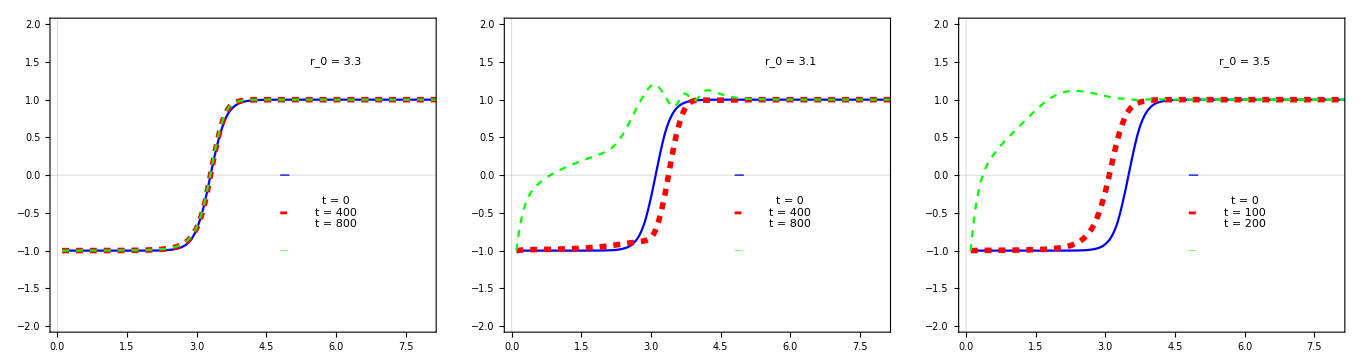
-Graphics-rΦ(r)

C:\Users\Leandros\Dropbox\diplomatikes-phd\george-alestas\project\tex-lp1

fig6.pdf

```mathematica
g[1]=Show[{sol0,sol400,sol800},Graphics[{Thick,Blue,Line[{{4.8,0},{5,0}}]}],Graphics[{Red,Thickness[0.005],Dashed,Line[{{4.8,-.5},{5,-.5}}]}],Graphics[{Green,Thickness[0.001],Dashed,Line[{{4.8,-1},{5,-1}}]}],Graphics[{Inset["t = 0\nt = 400\nt = 800",{6,-.5}]}],Graphics[{Inset["r_0 = 3.3",{6,1.5}]}],BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Large]];
g[2]=Show[{in0,in400,in800},Graphics[{Thick,Blue,Line[{{4.8,0},{5,0}}]}],Graphics[{Red,Thickness[0.005],Dashed,Line[{{4.8,-.5},{5,-.5}}]}],Graphics[{Green,Thickness[0.001],Dashed,Line[{{4.8,-1},{5,-1}}]}],Graphics[{Inset["t = 0\nt = 400\nt = 800",{6,-.5}]}],Graphics[{Inset["r_0 = 3.1",{6,1.5}]}],BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Large]];
g[3]=Show[{out0,out100,out200},Graphics[{Thick,Blue,Line[{{4.8,0},{5,0}}]}],Graphics[{Red,Thickness[0.005],Dashed,Line[{{4.8,-.5},{5,-.5}}]}],Graphics[{Green,Thickness[0.001],Dashed,Line[{{4.8,-1},{5,-1}}]}],Graphics[{Inset["t = 0\nt = 100\nt = 200",{6,-.5}]}],Graphics[{Inset["r_0 = 3.5",{6,1.5}]}],BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Large]];
pt1=Table[g[i],{m,1},{i,1,3}];

d1=Panel[plotGrid[pt1,1363,363],{"r",Rotate["Φ(r)",Pi/2]},{Bottom,Left},Background->White]
SetDirectory[NotebookDirectory[]]
Export["fig6.pdf",d1,ImageResolution->1000,ImageSize->Full]
```

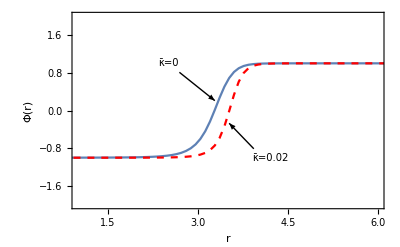

D:\Downloads

fig7.pdf

```mathematica
(*Figure 7: Plot of the comparison of static wall field solution in the presence and absence of backreaction*)
Clear[b,ll];
b=-0.255; ll=-0.202;
gr=r^2+2 b r^3 - ll r^4 /3;
Plot[gr,{r,0,6}];
imax=200;
rmin=0.0;
rmax=16;
dx=(rmax-rmin)/imax;
r[i_]:=i dx+rmin;
fp[i_]:=(f[i]-f[i-1])/dx;
e[i_]:=(r[i]^2 + 2 b r[i]^3-(ll/3) r[i]^4)fp[i]^2/2+r[i]^2(f[i]^2-1)^2 /4;
f[0]=-1;
f[imax]=1;
etot=dx  Sum[e[i],{i,1,imax}];
r0=10;
ft[x_]:=Tanh[5(x-r0)];
ftab=Table[{f[i],ft[r[i]]},{i,1,imax-1}];
sol1=FindMinimum[etot,ftab,MaxIterations->1000000,AccuracyGoal->6];
etot /. sol1[[2]];
tfsol=Table[{i dx+rmin,f[i]/. sol1[[2]]},{i,0,imax}];
plsol1=ListPlot[tfsol,Joined->True,PlotRange->All,Frame->True,FrameLabel->{r,Φ}];
ftfsol=Interpolation[tfsol];
fmet[r_]:=(1 + 2 b r-(ll/3) r^2);
aa=0.02;(*We set the Backreaction parameter value*)
rho1=0.5 fmet[r] D[ftfsol[r],r]+(ftfsol[r]^2-1)^2 /4;
rho2=aa rho1;
Plot[rho2,{r,0,8},PlotRange->All];
eq1=g3[r]/r^2+g3'[r]/r==rho2-4 b/r +ll;(*Einstein equation for energy density*)
rmin=0.0001;
grmin=0;
rmax=16;
ggsol=NDSolve[{eq1,g3[rmin]==0.0},g3[r],{r,rmin,rmax}];
pl2=Plot[r^2(1-Evaluate[g3[r]/.ggsol]),{r,rmin,rmax}];
gbr=(1-Evaluate[g3[r]/.ggsol]);
gbrc[x_]:=gbr[[1]]/. r->x
dx=(rmax-rmin)/imax;
r[i_]:=i dx+rmin;
fp[i_]:=(f[i]-f[i-1])/dx;
e[i_]:=(r[i]^2 gbrc[r[i]])fp[i]^2/2+r[i]^2(f[i]^2-1)^2 /4;
etot=dx  Sum[e[i],{i,1,imax}];
ft[x_]:=Tanh[5(x-r0)];
ftab=Table[{f[i],ft[r[i]]},{i,1,imax-1}];
sol1=FindMinimum[etot,ftab,MaxIterations->1000000,AccuracyGoal->6];
etot /. sol1[[2]];
tfsol=Table[{i dx+rmin,f[i]/. sol1[[2]]},{i,0,imax}];
plsol2=ListPlot[tfsol,Joined->True,PlotRange->All,PlotStyle->{Red,Dashed},Frame->True,FrameLabel->{r,Φ}];
solbnb=Show[plsol1,plsol2,Graphics[{Inset["κ̄=0",{2.5,1}]}],Graphics[{Arrow[{{2.69,0.81},{3.28,0.21}}]}],Graphics[{Inset["κ̄=0.02",{4.2,-1}]}],Graphics[{Arrow[{{3.93,-0.81},{3.52,-0.270}}]}],PlotStyle->{Red,Blue},PlotRange->{{1,6},{-2,2}},PlotTheme->"Scientific",BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Medium],Frame->True,FrameLabel-> {"r","Φ(r)"}]
SetDirectory[NotebookDirectory[]]
Export["fig7.pdf",solbnb,ImageResolution->1000]
Clear[h,h1,fmet]
fmet[r_]:=(1 + 2 b r-(ll/3) r^2);
h[r_,r0_]:=Tanh[3.1(r-r0)];
rhod[r0_]:=NIntegrate[r^2(0.5 fmet[r] D[h[r,r0],r]^2+(h[r,r0]^2-1)^2 /4 ),{r,rmin,rmax}];
```

```mathematica
(*Figure 8: Plot of the effect of backreaction on the energy functional*)
```

```mathematica
pl1=Plot[rhod[r0],{r0,rmin,4.5},PlotTheme->"Scientific",PlotStyle->Blue,PlotRange->All];
Clear[h,h1,fmet]
fmet[r_]:=gbrc[r];
h[r_,r0_]:=Tanh[3.1(r-r0)];
rhodbc[r0_]:=NIntegrate[r^2(0.5 gbrc[r] D[h[r,r0],r]^2+(h[r,r0]^2-1)^2 /4 ),{r,rmin,rmax}];
imax=100;
rmin1=0.1;
rmax1=4.5;
dx=(rmax1-rmin1)/imax;
trhodbc=Table[{i dx+rmin1,rhodbc[i dx+rmin1]},{i,0,imax}];
pl2=ListPlot[trhodbc,Joined->True,PlotTheme->"Scientific",PlotStyle->{Red,Dashed}];
```

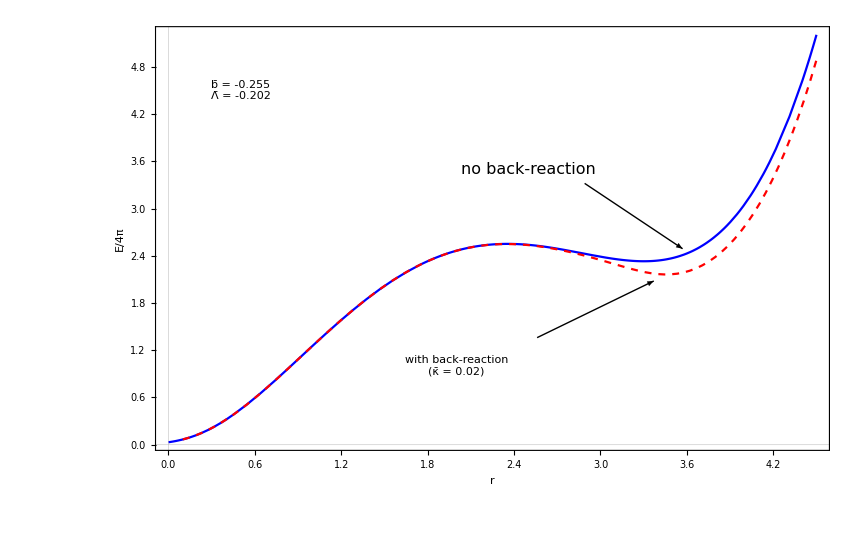

```mathematica
energ=Show[pl1,pl2,Graphics[{Inset["b̄ = -0.255\nΛ̄ = -0.202",{0.5,4.5}]}],Graphics[{Inset["no back-reaction",{2.5,3.5}]}],Graphics[{Arrow[{{2.89,3.32},{3.57,2.49}}]}],Graphics[{Inset["with back-reaction\n(κ̄ = 0.02)",{2,1}]}],Graphics[{Arrow[{{2.56,1.36},{3.37,2.08}}]}],PlotTheme->"Scientific",PlotRange->All,BaseStyle->{Medium,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",Medium],Frame->True,FrameLabel-> {"r","E/4π"}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["fig8.pdf",energ,ImageResolution->1000,ImageSize->Full]
```

fig8.pdf